```mathematica
Buc[r_,b_]:=b^(2/b-1)Exp[r^b/b]Gamma[2/b,r^b/b]/(r^b-2);
Bmin[b_]:=x/.FindMinimum[{Buc[x,b],x>2^(1/b)},{x,1}]⟦2⟧;
Pv[r_,b_,Ro_,Bu_]:=(1+Ro(2-r^b)Exp[(1-r^b)/b])/(1-Ro/Bu Exp[1/b] b^(2/b-1)Gamma[2/b,r^b/b])-1;
Vort[r_,b_]:=(2-r^b)Exp[(1-r^b)/b];
PvShield[b_,Ro_,Bu_]:=Module[{rstar,PvPositive,PvTotal},
If[b<1&&Bu<Buc[Bmin[b],b],
0,
rstar=r/.FindRoot[Pv[r,b,Ro,Bu]==0,{r,1}];
PvPositive=NIntegrate[r Pv[r,b,Ro,Bu],{r,0,rstar}];
PvTotal=NIntegrate[r Pv[r,b,Ro,Bu],{r,0,20}];
1-PvTotal/PvPositive]
];
```

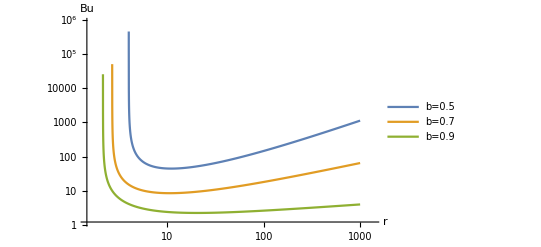

```mathematica
LogLogPlot[{Buc[r,0.5],Buc[r,0.7],Buc[r,0.9]},{r,2,1000},
AxesLabel->{Style["r",Bold,18],Style["Bu",Bold,18]},
PlotLegends->{Style["b=0.5",Bold,16],
Style["b=0.7",Bold,16],
Style["b=0.9",Bold,16]}]
```

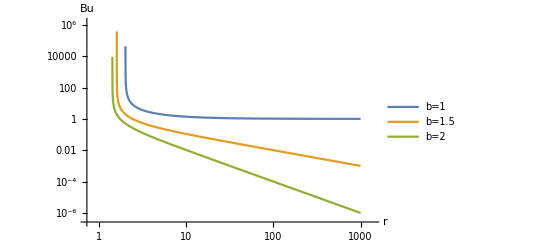

```mathematica
LogLogPlot[{Buc[r,1],Buc[r,1.5],Buc[r,2]},{r,1,1000},
AxesLabel->{Style["r",Bold,18],Style["Bu",Bold,18]},
PlotLegends->{Style["b=1",Bold,16],
Style["b=1.5",Bold,16],
Style["b=2",Bold,16]}]
```

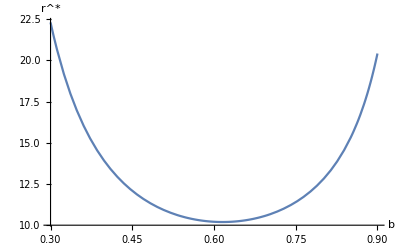

```mathematica
Plot[Bmin[b],{b,0.3,0.9},AxesLabel->{Style["b",Bold,18],Style["r^*",Bold,18]}]
```

ReplaceAll::reps: {x, 1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::exclul: {Im[b] - 0, Im[x/. {x, 1}] - 0, Im[x/. {x, 1}] - 0} must be a list of equalities or real-valued functions.

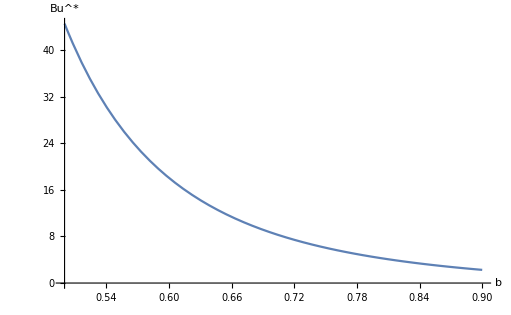

```mathematica
Plot[Buc[Bmin[b],b],{b,0.5,0.9},AxesLabel->{Style["b",Bold,18],Style["Bu^*",Bold,18]}]
```

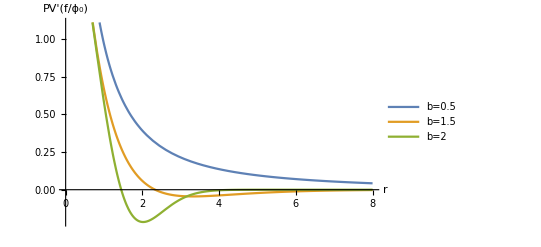

```mathematica
Plot[{Pv[r,0.5,0.5,10],Pv[r,1,0.5,10],Pv[r,2,0.5,10]},{r,0,8},
AxesLabel->{Style["r",Bold,18],Style["PV'(f/ϕ_0)",Bold,18]},
PlotLegends->{Style["b=0.5",Bold,16],
Style["b=1.5",Bold,16],
Style["b=2",Bold,16]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

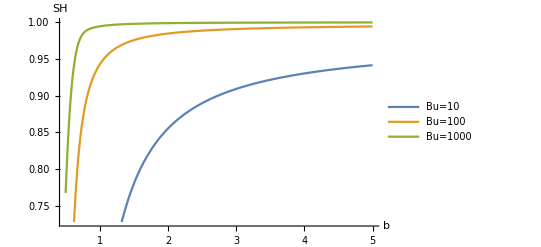

```mathematica
Plot[{PvShield[b,0.2,10],PvShield[b,0.2,100],PvShield[b,0.2,1000]},{b,0.5,5},
AxesLabel->{Style["b",Bold,18],Style["SH",Bold,18]},
PlotLegends->{Style["Bu=10",Bold,16],
Style["Bu=100",Bold,16],
Style["Bu=1000",Bold,16]}]
```

```mathematica
Buc[Bmin[0.5],0.5]
```

44.5893

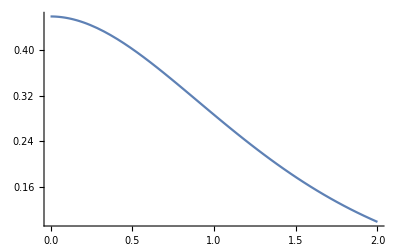

```mathematica
Plot[//.b->1.5,{r,0,2}]
```

```mathematica
F[r_,b_]:=0.2*Exp[1/b] b^(2/b-1)Gamma[2/b,r^b/b]+0.2^2(E/2)^(2/b)b^(2/b-1)Gamma[2/b,2 r^b/b]
```

```mathematica
F[0,1.5]
```

0.459755

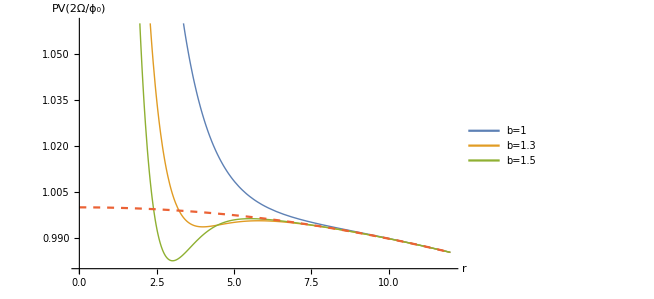

```mathematica
Pv[r_,b_,Ro_,Bu_]:=(1+Ro(2-r^b)Exp[(1-r^b)/b])/(1-Ro/Bu Exp[1/b] b^(2/b-1)Gamma[2/b,r^b/b]);
ϕ[r_,b_,Ro_,Bu_]:=(1-Ro/Bu Exp[1/b] b^(2/b-1)Gamma[2/b,r^b/b])
beta=0.5*(1000/70000)^2;
Plot[{Pv[r,1.,0.2,1]-beta*r^2/ϕ[r,1.,0.2,1],Pv[r,1.3,0.2,1]-beta*r^2/ϕ[r,1.3,0.2,1],Pv[r,1.5,0.2,1]-beta*r^2/ϕ[r,1.5,0.2,1],1-beta*r^2},{r,0,12},
AxesLabel->{Style["r",Bold,18],Style["PV(2Ω/ϕ_0)",Bold,18]},
PlotLegends->Placed[{Style["b=1",Bold,16],
Style["b=1.3",Bold,16],
Style["b=1.5",Bold,16]},{Right,Top}],
PlotRange->{{0.98,1.06}},
PlotStyle->{Thick,Thick,Thick,Dashed},
TicksStyle->Directive["Label", 16],
AxesStyle->Thick]
```

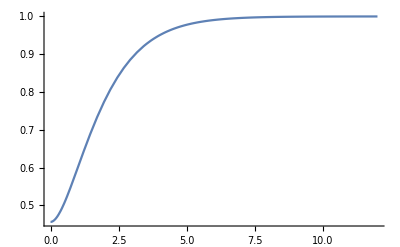

```mathematica
Plot[ϕ[r,1.,0.2,1],{r,0,12}]
```

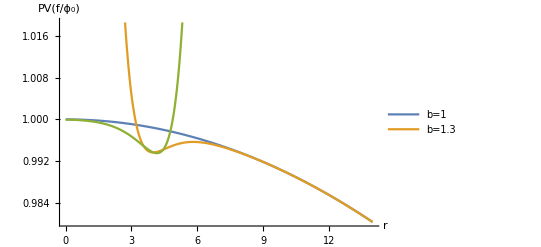

```mathematica
Plot[{1-1*^-4*r^2,Pv[r,1.3,0.2,1]-1*^-4*r^2,Pv[8-r,1.3,0.2,1]-1*^-4*r^2},{r,0,14},
AxesLabel->{Style["r",Bold,18],Style["PV(f/ϕ_0)",Bold,18]},
PlotLegends->{Style["b=1",Bold,18],
Style["b=1.3",Bold,18]}]
```

```mathematica
Rpv[r_,b_]:=(2-r^b)Exp[(1-r^b)/b]
```

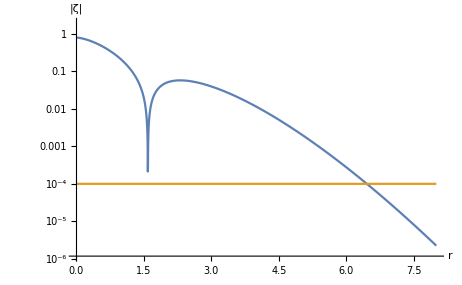

```mathematica
LogPlot[{Abs[0.2*Rpv[r,1.5]],1*^-4},{r,0,8},AxesLabel->{Style["r",16],Style["|ζ|",16]}]
```